# Quantum gates and computation.

## My notations for this notebook : ket[{0}] and ket[{1}] stand for Dirac’s ket representation, |0> and |1>. Their matrix representation are |0>={1,0} and |1>={0,1}. More generally : ket[{0,1,0}] stands for Dirac’s ket representation, |010>.

## Ket to Matrix represention :

```mathematica
BasisKetToMat[ket_]:=ReplacePart[Table[0,{k,2^Length[ket[[1]]]}],1,1+FromDigits[ket[[1]],2]]
```

```mathematica
KTM[x_  ket[y_]]:=x BasisKetToMat[ket[y]]
```

```mathematica
KTM[ket[y_]]:= BasisKetToMat[ket[y]]
```

```mathematica
KetToMat[ket_]:=Distribute[KTM[ket]]
```

```mathematica
(*3 Examples : *)     {KetToMat[  ket[{1}]],KetToMat[  ket[{0,1}]],KetToMat[  ket[{0,1}]+1/(√2) ket[{1,0}]+a  ket[{1,1}]]}
```

{{0,1},{0,1,0,0},{0,1,1/(√2),a}}

## Matrix to Ket representation :

```mathematica
MatToKet[list_]:=Sum[{list[[k]] ket[IntegerDigits[Position[UnitVector[Length[list],k],1][[1,1]]-1,2,Log[2,Length[UnitVector[Length[list],k]]]]] },{k,Length[list]}][[1]]
```

```mathematica
(*3 Examples : *)    {MatToKet[{0,1}],MatToKet[{0,1,0,0}],MatToKet[{0,1,1/(√2),a}]}
```

{ket[{1}],ket[{0,1}],ket[{0,1}]+ket[{1,0}]/(√2)+a ket[{1,1}]}

## External product |ket><bra| via matrix representation :

```mathematica
x_ ⊗ y_:=ArrayFlatten[Outer[Times,x,y]]
```

```mathematica
(* Example : *)    Subscript[D, i_]:= KetToMat[ket[{i}]]⊗KetToMat[ket[{i}]]          (* Equivalent to |1><1| in matrix form *)
```

```mathematica
{Subscript[D, 0],Subscript[D, 1],Subscript[D, 0]//MatrixForm ,Subscript[D, 1]//MatrixForm }                (* Representations of '0' or '1' detectors *)
```

{{{1,0},{0,0}},{{0,0},{0,1}},(1 | 0
0 | 0),(0 | 0
0 | 1)}

```mathematica
{Subscript[D, 0].{1,0},Subscript[D, 1].{1,0},Subscript[D, 0].{0,1},Subscript[D, 1].{0,1}}      (* Confirms that Subscript[D, i] detects |i> with probability one *)
```

{{1,0},{0,0},{0,0},{0,1}}

## Tensor product |ket1>|ket2> via matrix representation :

```mathematica
Flatten[KetToMat[ket[{1}]]⊗KetToMat[ket[{1}]]]     (*The same "Outer" plus "Flatten" does the expected job : there is little syntactic diference between both products *)
```

{0,0,0,1}

```mathematica
MatToKet[Flatten[KetToMat[ket[{1}]]⊗KetToMat[ket[{1}]]]]        (* In agreement with  |1>|1> = |11>  *)
```

ket[{1,1}]

## Some useful gates acting on a single qubit : Hadamard (H), Dephasing (F), Not (M) :

```mathematica
H=1/(√2)({{1, 1}, {1, -1}});Φ[φ_]:=({{1, 0}, {0, ⅇ^(ⅈ φ)}});M=({{0, 1}, {1, 0}});
```

Example : a balanced Mach - Zehnder interferometer :

```mathematica
H.M.H//MatrixForm
```

(1 | 0
0 | -1)

## Pauli and rotation matrices :

```mathematica
Subscript[σ, x]=({{0, 1}, {1, 0}});Subscript[σ, y]=({{0, -ⅈ}, {ⅈ, 0}});Subscript[σ, z]=({{1, 0}, {0, -1}});
```

```mathematica
Rx[θ_]:=MatrixExp[ⅈ θ Subscript[σ, x]];Ry[θ_]:=MatrixExp[ⅈ θ Subscript[σ, y]];Rz[θ_]:=MatrixExp[ⅈ θ Subscript[σ, z]];
```

## Preparation of a single qubit in an arbitrary state (starting with | 0 >= {1, 0}) ; U does the job up to an inessential phase :

```mathematica
U[φ_,θ_]:= Φ[φ+π/2].H.Φ[θ].H
```

```mathematica
U[φ,θ]==ⅇ^(ⅈ θ/2) ({{Cos[θ/2], -ⅈ Sin[θ/2]}, {ⅇ^(ⅈ φ)  Sin[θ/2], ⅈ ⅇ^(ⅈ φ) Cos[θ/2]}})//Simplify
```

True

## Every gate can be reduced to H and F (H and F are universal for a single qubit) :

```mathematica
Rx[θ]==ⅇ^(ⅈ θ) H.Φ[-2θ].H//Simplify
```

True

```mathematica
Ry[θ]==ⅇ^(ⅈ θ) Φ[π/2].H.Φ[-2θ].H.Φ[-π/2]//Simplify
```

True

```mathematica
{Rx[θ],Ry[θ]}
```

{{{Cos[θ],ⅈ Sin[θ]},{ⅈ Sin[θ],Cos[θ]}},{{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}}

## Altering the polarization state of a single photon with a plate L_(β,δ) :

```mathematica
L[β_,δ_]:= ({{ⅇ^(ⅈ δ/2)Cos[β]^2+ⅇ^(-ⅈ δ/2)Sin[β]^2, ⅈ Sin[2β] Sin[δ/2]}, {ⅈ Sin[2β] Sin[δ/2], ⅇ^(-ⅈ δ/2)Cos[β]^2+ⅇ^(ⅈ δ/2)Sin[β]^2}})
```

Typical examples (up to an inessential phase) :

```mathematica
L[0,δ]//MatrixForm           (*A dephasing gate*)
```

(ⅇ^((ⅈ δ)/2) | 0
0 | ⅇ^(-(ⅈ δ)/2))

```mathematica
L[π/4,π/2]//Simplify//MatrixForm           (*Sqrt of Not gate which transforms linear polarization to circular polarization*)
```

(1/(√2) | ⅈ/(√2)
ⅈ/(√2) | 1/(√2))

```mathematica
L[π/4,π/2].L[π/4,π/2]//ExpToTrig//MatrixForm        (*Not gate, up to factor i, results of the squaring of the former gate*)
```

(0 | ⅈ
ⅈ | 0)

```mathematica
L[π/8,π]//Simplify//MatrixForm              (*Hadamard gate*)
```

(ⅈ/(√2) | ⅈ/(√2)
ⅈ/(√2) | -ⅈ/(√2))

```mathematica
L[π/4,π]//Simplify//MatrixForm           (*Not gate*)
```

(0 | ⅈ
ⅈ | 0)

## Special case : rotating the linear polarization of a photon (Zeno effect) :

```mathematica
Subscript[D, 0].{1,0}
```

{1,0}

```mathematica
Ry[θ]//MatrixForm
```

(Cos[θ] | Sin[θ]
-Sin[θ] | Cos[θ])

```mathematica
Abs[Subscript[D, 0].MatrixPower[Ry[ π/(2n)],n].{1,0}//FullSimplify//PowerExpand]
```

{0,0}

```mathematica
Abs[Subscript[D, 0].MatrixPower[Subscript[D, 0].Ry[ π/(2n)],n].{1,0}//FullSimplify//PowerExpand]
```

{Abs[Cos[π/(2 n)]^n+2 (0^(2+n)+0^(1+n) Tan[π/(2 n)])],2 Abs[0^(2+n) (1+Tan[π/(2 n)])]}

## Gates acting on registers (at least two qubits). This needs tensor products :

```mathematica
IdentityMatrix[2]⊗ {{a,b},{d,e}}//MatrixForm
```

(a | b | 0 | 0
d | e | 0 | 0
0 | 0 | a | b
0 | 0 | d | e)

The Controlled-Not gate (C-Not) :

```mathematica
CNot=Subscript[D, 0]⊗IdentityMatrix[2]+Subscript[D, 1]⊗M;
```

```mathematica
CNot//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

The Swap gate (Sw) :

```mathematica
Sw=CNot.(IdentityMatrix[2]⊗Subscript[D, 0]+M⊗Subscript[D, 1]).CNot
```

{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}

The Controlled-Controlled-Not gate (CC-Not) :

```mathematica
CCNot=(Subscript[D, 0]⊗Subscript[D, 0])⊗IdentityMatrix[2]+(Subscript[D, 0]⊗Subscript[D, 1])⊗IdentityMatrix[2]+(Subscript[D, 1]⊗Subscript[D, 0])⊗IdentityMatrix[2]+(Subscript[D, 1]⊗Subscript[D, 1])⊗M;
```

```mathematica
CCNot//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

Preparation of a 3 qubits register starting with |000> :

```mathematica
((Ry[-π/4]⊗Ry[-π/4])⊗Ry[-ArcTan[2]]).{1,0,0,0,0,0,0,0}//MatrixForm           (*Encodes the sequence {1,2,1,2,1,2,1,2} for future use*)
```

(1/(2 √5)
1/(√5)
1/(2 √5)
1/(√5)
1/(2 √5)
1/(√5)
1/(2 √5)
1/(√5))

```mathematica
MatToKet[((Ry[-π/4]⊗Ry[-π/4])⊗Ry[-ArcTan[2]]).{1,0,0,0,0,0,0,0}]
```

ket[{0,0,0}]/(2 √5)+ket[{0,0,1}]/(√5)+ket[{0,1,0}]/(2 √5)+ket[{0,1,1}]/(√5)+ket[{1,0,0}]/(2 √5)+ket[{1,0,1}]/(√5)+ket[{1,1,0}]/(2 √5)+ket[{1,1,1}]/(√5)

```mathematica
∑_(k=0)^7 (1+Mod[k,2])u^k                      (*The factorization of the associated generating function detects if the register is separable*)
```

1+2 u+u^2+2 u^3+u^4+2 u^5+u^6+2 u^7

```mathematica
Factor[∑_(k=0)^7 (1+Mod[k,2])u^k]               (*The register is of course separable*)
```

(1+2 u) (1+u^2) (1+u^4)

```mathematica
Sum[u^k(1+Mod[k,4]),{k,0,15}]
```

1+2 u+3 u^2+4 u^3+u^4+2 u^5+3 u^6+4 u^7+u^8+2 u^9+3 u^10+4 u^11+u^12+2 u^13+3 u^14+4 u^15

```mathematica
Factor[Sum[u^k(1+Mod[k,4]),{k,0,15}]]             (*The corresponding register is not fully separable*)
```

(1+2 u+3 u^2+4 u^3) (1+u^4) (1+u^8)

Detection projectors for a particular qubit in the register (two qubits in the example) :

```mathematica
{Subscript[D, 0]⊗Subscript[D, 0]//MatrixForm,Subscript[D, 0]⊗Subscript[D, 1]//MatrixForm,Subscript[D, 1]⊗Subscript[D, 0]//MatrixForm,Subscript[D, 1]⊗Subscript[D, 1]//MatrixForm}
```

{(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)}

Controlled-U gates (C-SqrtNot in the example) :

```mathematica
SqrtNot=ⅇ^(-ⅈ π/4) L[π/4,π/2]//ExpToTrig
```

{{1/2-ⅈ/2,1/2+ⅈ/2},{1/2+ⅈ/2,1/2-ⅈ/2}}

```mathematica
SqrtNot==ⅇ^(-ⅈ π/4)Φ[π/2].H.Φ[π/2]//Simplify
```

True

```mathematica
CSqrtNot=Subscript[D, 0]⊗IdentityMatrix[2]+Subscript[D, 1]⊗SqrtNot
```

{{1,0,0,0},{0,1,0,0},{0,0,1/2-ⅈ/2,1/2+ⅈ/2},{0,0,1/2+ⅈ/2,1/2-ⅈ/2}}

C-Phase and C-H gates :

```mathematica
CΦ[φ_]:=Subscript[D, 0]⊗IdentityMatrix[2]+Subscript[D, 1]⊗Φ[φ]         (*Controlled Phase gate*)
```

```mathematica
CΦ[φ]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅇ^(ⅈ φ))

```mathematica
CH=Subscript[D, 0]⊗IdentityMatrix[2]+Subscript[D, 1]⊗H //MatrixForm         (*Controlled Hadamard gate*)
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1/(√2) | 1/(√2)
0 | 0 | 1/(√2) | -1/(√2))

Reduction of the C-Not gate to Hadamard and C-Phase gates :

```mathematica
CNot==(IdentityMatrix[2]⊗H).CΦ[π/2].CΦ[π/2].(IdentityMatrix[2]⊗H)//Simplify
```

True

Reduction of the CC-Not (3 qubits) to Hadamard, CNot and C-Phase gates :

```mathematica
CCNot==(IdentityMatrix[4]⊗H).(Subscript[D, 0]⊗IdentityMatrix[4]+(Subscript[D, 1]⊗IdentityMatrix[2])⊗Φ[π/2]).(CNot⊗IdentityMatrix[2]).(IdentityMatrix[2]⊗CΦ[-π/2]).(CNot⊗IdentityMatrix[2]).(IdentityMatrix[2]⊗CΦ[π/2]).(IdentityMatrix[4]⊗H)
```

True

CCNot + CNot gates acting as a binary  half-adder

```mathematica
halfadder[ket[{x_,y_,0}]]:=MatToKet[(CNot⊗IdentityMatrix[2]).CCNot.KetToMat[ket[{x,y,0}]]]
```

```mathematica
{halfadder[ket[{0,0,0}]],halfadder[ket[{0,1,0}]],halfadder[ket[{1,0,0}]],halfadder[ket[{1,1,0}]]}
```

{ket[{0,0,0}],ket[{0,1,0}],ket[{1,1,0}],ket[{1,0,1}]}

Identification algorithm among 4 (out of 16 existing) operators (reversibly) calculating Boolean functions in two variables (following the quantum scheme : |a>|b>|0> -> |a>|b>|f(a,b)>)

```mathematica
and=CCNot;xlessthany=CCNot.(IdentityMatrix[2]⊗CNot);xgreaterthany=CCNot.(Subscript[D, 1]⊗IdentityMatrix[4]+(Subscript[D, 1]⊗IdentityMatrix[2])⊗M);nor=(IdentityMatrix[4]⊗M).(Subscript[D, 0]⊗IdentityMatrix[4]+(Subscript[D, 1]⊗IdentityMatrix[2])⊗M).CCNot.(IdentityMatrix[2]⊗CNot);
```

```mathematica
Table[MatToKet[nor.KetToMat[ket[{i,j,0}]] ],{i,0,1},{j,0,1}]     (*The result translated with kets : the third qubit is the Nor of the two first*)
```

{{ket[{0,0,1}],ket[{0,1,0}]},{ket[{1,0,0}],ket[{1,1,0}]}}

```mathematica
Deutsch[op_]=((H⊗H)⊗IdentityMatrix[2]).(CΦ[π]⊗IdentityMatrix[2]).((Φ[π]⊗Φ[π])⊗IdentityMatrix[2]).((H⊗H)⊗IdentityMatrix[2]).op.((H⊗H)⊗H);       (*Identification algorithm in one pass between 4 boolean predefined functions*)
```

```mathematica
Deutsch[and].KetToMat[ket[{0,0,1}]]     (*The 2 first qubits of the result,|11>1/(√2)(|0>-|1>), is the signature of and*)
```

{0,0,0,0,0,0,1/(√2),-1/(√2)}

```mathematica
Deutsch[nor].KetToMat[ket[{0,0,1}]]        (*The 2 first qubits of the result,|00>1/(√2)(|0>-|1>), is the signature of nor*)
```

{1/(√2),-1/(√2),0,0,0,0,0,0}

```mathematica
Deutsch[xlessthany].KetToMat[ket[{0,0,1}]]     (*The 2 first qubits of the result,|01>1/(√2)(|0>-|1>), is the signature of a<b*)
```

{0,0,1/(√2),-1/(√2),0,0,0,0}

```mathematica
Deutsch[xgreaterthany].KetToMat[ket[{0,0,1}]]     (*The 2 first qubits of the result,|10>1/(√2)(|0>-|1>), is the signature of a>b*)
```

{0,0,0,0,0,0,0,0}

Grover algorithm   (Lorsque n=2 qubits sont en jeu une seule itération suffit à localiser l’élément intrus (incarné par un changement de signe : -1 dans une bande de 1 (Une porte CCNot trafiquée fait l’affaire)) sinon il en faut Sqrt(n).

```mathematica
2 Subscript[D, 0]-IdentityMatrix[2]
```

{{1,0},{0,-1}}

```mathematica
2 Subscript[D, 1]-IdentityMatrix[2]
```

{{-1,0},{0,1}}

```mathematica
Grover[op_]=((H⊗H)⊗IdentityMatrix[2]).((2 Subscript[D, 0]⊗Subscript[D, 0]-IdentityMatrix[4])⊗IdentityMatrix[2]).((H⊗H)⊗IdentityMatrix[2]).op.((H⊗H)⊗H);
```

```mathematica
CCNot=(Subscript[D, 0]⊗Subscript[D, 0])⊗IdentityMatrix[2]+(Subscript[D, 0]⊗Subscript[D, 1])⊗IdentityMatrix[2]+(Subscript[D, 1]⊗Subscript[D, 0])⊗IdentityMatrix[2]+(Subscript[D, 1]⊗Subscript[D, 1])⊗M;   (*Pour rappel*)
```

```mathematica
Grover[CCNot].KetToMat[ket[{0,0,1}]]      (*The 2 first qubits of the result,|11>1/(√2)(|0>-|1>), indicate which item produces a change of sign (11 in the case of the CCNot gate)*)
```

{0,0,0,0,0,0,1/(√2),-1/(√2)}

```mathematica
Grover[(Subscript[D, 0]⊗Subscript[D, 0])⊗IdentityMatrix[2]+(Subscript[D, 0]⊗Subscript[D, 1])⊗IdentityMatrix[2]+(Subscript[D, 1]⊗Subscript[D, 0])⊗M+(Subscript[D, 1]⊗Subscript[D, 1])⊗IdentityMatrix[2]].KetToMat[ket[{0,0,1}]]
```

{0,0,0,0,1/(√2),-1/(√2),0,0}

```mathematica
Grover[(Subscript[D, 0]⊗Subscript[D, 0])⊗IdentityMatrix[2]+(Subscript[D, 0]⊗Subscript[D, 1])⊗M+(Subscript[D, 1]⊗Subscript[D, 0])⊗IdentityMatrix[2]+(Subscript[D, 1]⊗Subscript[D, 1])⊗IdentityMatrix[2]].KetToMat[ket[{0,0,1}]]
```

{0,0,1/(√2),-1/(√2),0,0,0,0}

```mathematica
Grover[(Subscript[D, 0]⊗Subscript[D, 0])⊗M+(Subscript[D, 0]⊗Subscript[D, 1])⊗IdentityMatrix[2]+(Subscript[D, 1]⊗Subscript[D, 0])⊗IdentityMatrix[2]+(Subscript[D, 1]⊗Subscript[D, 1])⊗IdentityMatrix[2]].KetToMat[ket[{0,0,1}]]
```

{1/(√2),-1/(√2),0,0,0,0,0,0}

Shor algorithm

Quantum circuit for the Discrete Fourier Transform :

```mathematica
Subscript[DFT, 2]=Sw.(IdentityMatrix[2]⊗H) .CΦ[π/2].(H⊗IdentityMatrix[2]);     (*valid for a two-qubits register : be careful with the order*)
```

```mathematica
Subscript[DFT, 2]==1/(√(2^2))Table[Exp[(2ⅈ π)/2^2 j k],{j,0,2^2-1},{k,0,2^2-1}]
```

True

Probabilities of measuring one of the 4 possible output-states (in the order 00 01 10 11) :

```mathematica
resu=Subscript[DFT, 2].KetToMat[Subscript[s, 0]  ket[{0,0}] +Subscript[s, 1] ket[{0,1}]+Subscript[s, 2]  ket[{1,0}]+Subscript[s, 3]  ket[{1,1}]]
```

{s_0/2+s_1/2+s_2/2+s_3/2,s_0/2+(ⅈ s_1)/2-s_2/2-(ⅈ s_3)/2,s_0/2-s_1/2+s_2/2-s_3/2,s_0/2-(ⅈ s_1)/2-s_2/2+(ⅈ s_3)/2}

```mathematica
resu Conjugate[resu]//ComplexExpand//Simplify
```

{1/4 (s_0+s_1+s_2+s_3)^2,1/4 (s_0^2+s_1^2-2 s_0 s_2+s_2^2-2 s_1 s_3+s_3^2),1/4 (s_0-s_1+s_2-s_3)^2,1/4 (s_0^2+s_1^2-2 s_0 s_2+s_2^2-2 s_1 s_3+s_3^2)}

```mathematica
Subscript[DFT, 3]=((Sw⊗IdentityMatrix[2]).(IdentityMatrix[2]⊗Sw).(Sw⊗IdentityMatrix[2])).(IdentityMatrix[4]⊗H).(IdentityMatrix[2]⊗CΦ[π/2]).(Subscript[D, 0]⊗IdentityMatrix[4]+(Subscript[D, 1]⊗IdentityMatrix[2])⊗Φ[π/4] ).((IdentityMatrix[2]⊗H)⊗IdentityMatrix[2]).(CΦ[π/2]⊗IdentityMatrix[2]).(H⊗IdentityMatrix[4]);   (*valid for a three-qubits register : be careful with the order*)
```

```mathematica
Subscript[DFT, 3]==1/(√(2^3))Table[Exp[(2ⅈ π)/2^3 j k],{j,0,2^3-1},{k,0,2^3-1}]
```

True

```mathematica
resu=Subscript[DFT, 3].KetToMat[Subscript[s, 0]  ket[{0,0,0}] +Subscript[s, 1]  ket[{0,0,1}] +Subscript[s, 2]  ket[{0,1,0}] +Subscript[s, 3]  ket[{0,1,1}] +Subscript[s, 4]  ket[{1,0,0}] +Subscript[s, 5]  ket[{1,0,1}] +Subscript[s, 6]  ket[{1,1,0}] +Subscript[s, 7]  ket[{1,1,1}]]//Factor
```

{(s_0+s_1+s_2+s_3+s_4+s_5+s_6+s_7)/(2 √2),(s_0+(-1)^(1/4) s_1+ⅈ s_2+(-1)^(3/4) s_3-s_4-(-1)^(1/4) s_5-ⅈ s_6-(-1)^(3/4) s_7)/(2 √2),(s_0+ⅈ s_1-s_2-ⅈ s_3+s_4+ⅈ s_5-s_6-ⅈ s_7)/(2 √2),(s_0+(-1)^(3/4) s_1-ⅈ s_2+(-1)^(1/4) s_3-s_4-(-1)^(3/4) s_5+ⅈ s_6-(-1)^(1/4) s_7)/(2 √2),(s_0-s_1+s_2-s_3+s_4-s_5+s_6-s_7)/(2 √2),(s_0-(-1)^(1/4) s_1+ⅈ s_2-(-1)^(3/4) s_3-s_4+(-1)^(1/4) s_5-ⅈ s_6+(-1)^(3/4) s_7)/(2 √2),(s_0-ⅈ s_1-s_2+ⅈ s_3+s_4-ⅈ s_5-s_6+ⅈ s_7)/(2 √2),(s_0-(-1)^(3/4) s_1-ⅈ s_2-(-1)^(1/4) s_3-s_4+(-1)^(3/4) s_5+ⅈ s_6+(-1)^(1/4) s_7)/(2 √2)}

Probabilities of measuring one of the 8 possible output-states (in the order 000 001 010 011 100 101 110 111) :

```mathematica
resu Conjugate[resu]//ComplexExpand//Simplify
```

{1/8 (s_0+s_1+s_2+s_3+s_4+s_5+s_6+s_7)^2,1/8 (s_0^2+s_1^2+s_2^2+√2 s_2 s_3+s_3^2+√2 s_3 s_4+s_4^2-√2 s_2 s_5+√2 s_4 s_5+s_5^2-2 s_2 s_6-√2 s_3 s_6+√2 s_5 s_6+s_6^2+s_1 (√2 s_2-√2 s_4-2 s_5-√2 s_6)-√2 s_2 s_7-2 s_3 s_7-√2 s_4 s_7+√2 s_6 s_7+s_7^2+s_0 (√2 s_1-√2 s_3-2 s_4-√2 s_5+√2 s_7)),1/8 (s_0^2+s_1^2+s_2^2+s_3^2-2 s_2 s_4+s_4^2-2 s_3 s_5+s_5^2+2 s_2 s_6-2 s_4 s_6+s_6^2-2 s_0 (s_2-s_4+s_6)+2 s_3 s_7-2 s_5 s_7+s_7^2-2 s_1 (s_3-s_5+s_7)),1/8 (s_0^2+s_1^2+s_2^2-√2 s_2 s_3+s_3^2-√2 s_3 s_4+s_4^2+√2 s_2 s_5-√2 s_4 s_5+s_5^2-2 s_2 s_6+√2 s_3 s_6-√2 s_5 s_6+s_6^2+s_1 (-√2 s_2+√2 s_4-2 s_5+√2 s_6)+√2 s_2 s_7-2 s_3 s_7+√2 s_4 s_7-√2 s_6 s_7+s_7^2+s_0 (-√2 s_1+√2 s_3-2 s_4+√2 s_5-√2 s_7)),1/8 (s_0-s_1+s_2-s_3+s_4-s_5+s_6-s_7)^2,1/8 (s_0^2+s_1^2+s_2^2-√2 s_2 s_3+s_3^2-√2 s_3 s_4+s_4^2+√2 s_2 s_5-√2 s_4 s_5+s_5^2-2 s_2 s_6+√2 s_3 s_6-√2 s_5 s_6+s_6^2+s_1 (-√2 s_2+√2 s_4-2 s_5+√2 s_6)+√2 s_2 s_7-2 s_3 s_7+√2 s_4 s_7-√2 s_6 s_7+s_7^2+s_0 (-√2 s_1+√2 s_3-2 s_4+√2 s_5-√2 s_7)),1/8 (s_0^2+s_1^2+s_2^2+s_3^2-2 s_2 s_4+s_4^2-2 s_3 s_5+s_5^2+2 s_2 s_6-2 s_4 s_6+s_6^2-2 s_0 (s_2-s_4+s_6)+2 s_3 s_7-2 s_5 s_7+s_7^2-2 s_1 (s_3-s_5+s_7)),1/8 (s_0^2+s_1^2+s_2^2+√2 s_2 s_3+s_3^2+√2 s_3 s_4+s_4^2-√2 s_2 s_5+√2 s_4 s_5+s_5^2-2 s_2 s_6-√2 s_3 s_6+√2 s_5 s_6+s_6^2+s_1 (√2 s_2-√2 s_4-2 s_5-√2 s_6)-√2 s_2 s_7-2 s_3 s_7-√2 s_4 s_7+√2 s_6 s_7+s_7^2+s_0 (√2 s_1-√2 s_3-2 s_4-√2 s_5+√2 s_7))}

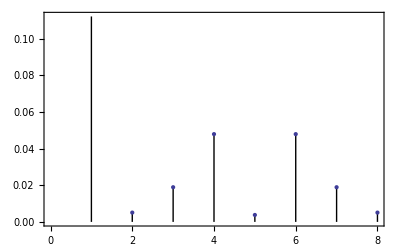

```mathematica
ListPlot[Chop[resu ComplexExpand[Conjugate[resu]]/.{Subscript[s, 0] ->1/(√33),Subscript[s, 1] ->2/(√33),Subscript[s, 2] ->3/(√33),Subscript[s, 3] ->1/(√33),Subscript[s, 4] ->2/(√33),Subscript[s, 5] ->3/(√33),Subscript[s, 6] ->1/(√33),Subscript[s, 7] ->2/(√33)}//N],Frame->True,Filling->Bottom,FillingStyle->Directive[Thick]]
```

```mathematica
Chop[resu ComplexExpand[Conjugate[resu]]/.{Subscript[s, 0] ->1/(√20),Subscript[s, 1] ->2/(√20),Subscript[s, 2] ->1/(√20),Subscript[s, 3] ->2/(√20),Subscript[s, 4] ->1/(√20),Subscript[s, 5] ->2/(√20),Subscript[s, 6] ->1/(√20),Subscript[s, 7] ->2/(√20)}//N]
```

{0.9,0,0,0,0.1,0,0,0}

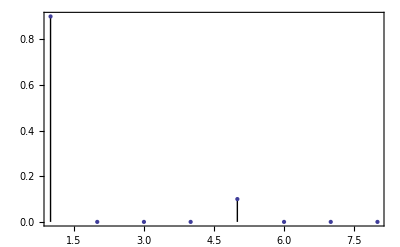

```mathematica
ListPlot[Chop[resu ComplexExpand[Conjugate[resu]]/.{Subscript[s, 0] ->1/(√20),Subscript[s, 1] ->2/(√20),Subscript[s, 2] ->1/(√20),Subscript[s, 3] ->2/(√20),Subscript[s, 4] ->1/(√20),Subscript[s, 5] ->2/(√20),Subscript[s, 6] ->1/(√20),Subscript[s, 7] ->2/(√20)}//N],PlotRange->All,Frame->True,Filling->Bottom,FillingStyle->Directive[Thick]]
```

```mathematica
Total[{0.8522727272727273,0.005087673297377347,0.018939393939393936,0.047942629732925686,0.003787878787878788,0.047942629732925665,0.018939393939393936,0.005087673297377346}]
```

1.

Random Quantum Walk

```mathematica
(*The following recursion computes the Feynman path-sum corresponding to the transit of a photon '0' in a triangular network of half-silvered plates. Additional phases are added so that the only alteration is a sign inversion when a plate is crossed in the South-North direction*)
```

```mathematica
c[0]=f[0,0];c[i_]:=c[i-1]/.f[x_,c_]->(f[x-1,0]+(-1)^c f[x+1,1])/(√2)//Simplify
```

```mathematica
c[1]
```

(f[-1,0]+f[1,1])/(√2)

```mathematica
c[2]
```

1/2 (f[-2,0]+f[0,0]+f[0,1]-f[2,1])

```mathematica
n=32;
```

```mathematica
(*Two additional functions are necessary in order to translate the results as detectors numbers*)
```

```mathematica
arg[a_ f_[x_,y_]]:=(n-1)y+(x+n)/2
```

```mathematica
treat[z_]:=If[ArrayQ[z],((n-1)z[[2]]+(z[[1]]+n)/2),z]
```

```mathematica
coeff=Table[Expand[c[n]][[k,1]],{k,2n}]
```

{1/65536,31/65536,1/65536,405/65536,29/65536,2871/65536,349/65536,11753/65536,2225/65536,26703/65536,7849/65536,26429/65536,13909/65536,-5225/65536,6421/65536,-17067/65536,-10183/65536,13179/65536,-1195/65536,121/65536,9217/65536,-9261/65536,-9151/65536,12045/65536,4741/65536,-11077/65536,77/65536,9009/65536,-3575/65536,-7293/65536,5577/65536,6435/65536,-6435/65536,-6435/65536,6435/65536,7007/65536,-5577/65536,-7579/65536,3575/65536,7227/65536,-77/65536,-4851/65536,-4741/65536,55/65536,9151/65536,5157/65536,-9217/65536,-5689/65536,1195/65536,-1463/65536,10183/65536,6099/65536,-6421/65536,4945/65536,-13909/65536,1679/65536,-7849/65536,297/65536,-2225/65536,27/65536,-349/65536,1/65536,-29/65536,-1/65536}

```mathematica
det=Table[treat[arg[2^n Expand[c[n]][[k]]]],{k,2n}]
```

{0,1,32,2,33,3,34,4,35,5,36,6,37,7,38,8,39,9,40,10,41,11,42,12,43,13,44,14,45,15,46,16,47,17,48,18,49,19,50,20,51,21,52,22,53,23,54,24,55,25,56,26,57,27,58,28,59,29,60,30,61,31,62,63}

```mathematica
probas=Flatten[Table[coeff[[Position[det,k][[1]]]],{k,0,2n-1}]]^2
```

{1/4294967296,961/4294967296,164025/4294967296,8242641/4294967296,138133009/4294967296,713050209/4294967296,698492041/4294967296,27300625/4294967296,291282489/4294967296,173686041/4294967296,14641/4294967296,85766121/4294967296,145082025/4294967296,122699929/4294967296,81162081/4294967296,53187849/4294967296,41409225/4294967296,41409225/4294967296,49098049/4294967296,57441241/4294967296,52229529/4294967296,23532201/4294967296,3025/4294967296,26594649/4294967296,32364721/4294967296,2140369/4294967296,37197801/4294967296,24453025/4294967296,2819041/4294967296,88209/4294967296,729/4294967296,1/4294967296,1/4294967296,841/4294967296,121801/4294967296,4950625/4294967296,61606801/4294967296,193460281/4294967296,41229241/4294967296,103693489/4294967296,1428025/4294967296,84953089/4294967296,83740801/4294967296,22477081/4294967296,5929/4294967296,12780625/4294967296,31102929/4294967296,41409225/4294967296,41409225/4294967296,31102929/4294967296,12780625/4294967296,5929/4294967296,22477081/4294967296,83740801/4294967296,84953089/4294967296,1428025/4294967296,103693489/4294967296,41229241/4294967296,193460281/4294967296,61606801/4294967296,4950625/4294967296,121801/4294967296,841/4294967296,1/4294967296}

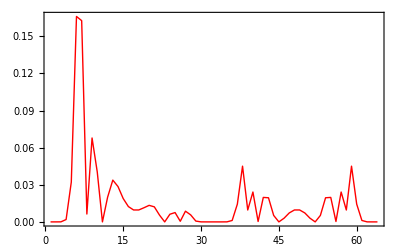

```mathematica
ListPlot[probas,PlotJoined->True,PlotStyle->{Thick,Red},Frame->True,PlotRange->All]
```

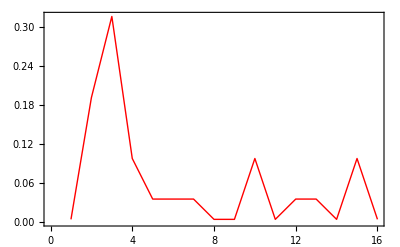

```mathematica
f1=ListPlot[{1,7,9,-5,3,-3,3,1,1,5,1,-3,3,-1,-5,-1}^2/256,PlotJoined->True,PlotStyle->{Thick,Red},Frame->True]
```

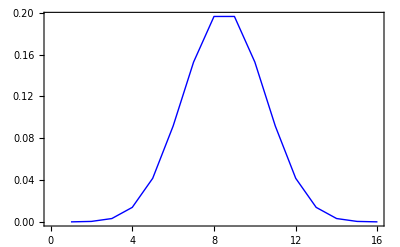

```mathematica
f2=ListPlot[Table[Binomial[15,k]/2^15,{k,0,15}],PlotJoined->True,PlotStyle->{Thick,Blue},Frame->True]
```

```mathematica
Sum[Binomial[15,k]/2^15,{k,0,15}]
```

1

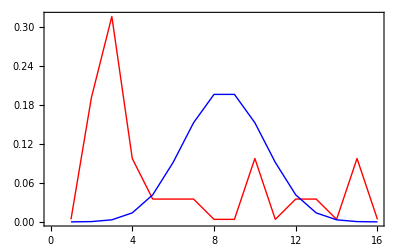

```mathematica
Show[{f1,f2}]
```